```mathematica
Manipulate[
Module[{y1,x0,yN1,yeq,yinlet,sol,check,check2,stage,test,n,steps,stepping,points,subtract,data,skip},
y1=10;x0=0;
yN1[x_]:=m2*x+y1;
yeq[x_]:=m1*x;
yinlet:=C0;

sol=x/.Solve[yeq[x]==yinlet,x][[1]];
check=x/.Solve[yN1[x]==yinlet,x][[1]];
check2=x/.Solve[yeq[x]==yN1[x],x][[1]];
stage[1]=x/.Solve[yeq[x]==y1,x][[1]];

Do[stage[i]=x/.Solve[yeq[x]==yN1[stage[i-1]],x][[1]],{i,2,100}];
test=Table[stage[n],{n,1,50}];

n=1;While[test[[n]]<check∧If[check2>0,yeq[check2]>yinlet,True],n++];

steps=Flatten[Table[{{test[[i]],yeq[test[[i]]]},{test[[i]],yN1[test[[i]]]}},{i,1,n}],1];
stepping=ReplacePart[Join[{{0,y1}},steps],{2*n+1,2}->C0];

(*Show[
Plot[{yN1[x],yeq[x],yinlet},{x,0,1.3},PlotStyle->{{Thick,Black},{Thick,Blue},{Thick,Dashed,RGBColor[0,0.7,0]}},PlotRange->{{0,1.3},{0,120}},
Frame->True,LabelStyle->{17,Black},ImageSize->{450,425},AspectRatio->Full,
Epilog->{
If[yN1[check2]>yinlet∨check2<0,{
Line@stepping(*,
Text[Style[#,16],{stage[#]+0.025,yeq[stage[#]]-3}]&/@Range@n*)}]
}],
ListPlot[Evaluate[Module[{i=0},MapAt[Callout[#,Style[++i,15]]&,2;; ;;2]@stepping](*[[#]]&/@Range[2,Length@stepping,2]*)],Joined->True,PlotStyle->Directive[Thin,Black]]
]*)
(*N@Module[{i=0},MapAt[Callout[#,Style[++i,16]]&,2;; ;;2]@stepping]*)
(*Module[{i=0},MapAt[Callout[#,Style[++i,16]]&,2;; ;;2]@stepping](*[[#]]&/@Range[1,Length@stepping,2]*)*)

Plot[{yN1[x],yeq[x],yinlet},{x,0,1.3},PlotStyle->{{Thick,Black},{Thick,Blue},{Thick,Dashed,RGBColor[0,0.7,0]}},PlotRange->{{0,1.3},{0,120}},
Frame->True,LabelStyle->{17,Black},ImageSize->{450,425},AspectRatio->Full,
Epilog->{
If[yN1[check2]>yinlet∨check2<0,{
Line@stepping,
Text[Style[#,16],{stage[#]+0.025,yeq[stage[#]]-3}]&/@Range@If[n≤15,n,15]}]
}]
],
Grid[{
{Control[{{C0,100,"inlet concentration (ppm)"},40,120,1,Appearance->"Labeled"}],SpanFromLeft},
{Control[{{m1,86},84,108,1,Appearance->"Labeled",ImageSize->Small}],
Control[{{m2,80},50,300,1,Appearance->"Labeled",ImageSize->Small}]}
},Alignment->Left]
]
```

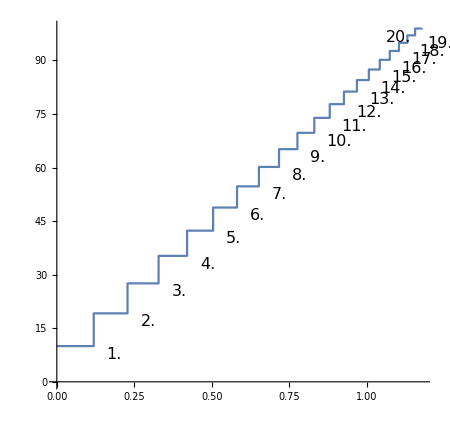

```mathematica
Module[{data},
data={{0.,10.},Callout[{0.119,10.},1.],{0.119,19.17},Callout[{0.228,19.17},2.],{0.228,27.57},Callout[{0.328,27.57},3.],{0.328207671957672,35.27199074074074},Callout[{0.419904651675485,35.27199074074074},4.],{0.419904651675485,42.33265817901235},Callout[{0.5039602164168137,42.33265817901235},5.],{0.5039602164168137,48.80493666409465},Callout[{0.5810111507630316,48.80493666409465},6.],{0.5810111507630316,54.73785860875343},Callout[{0.6516411739137313,54.73785860875343},7.],{0.6516411739137313,60.17637039135731},Callout[{0.7163853618018727,60.17637039135731},8.],{0.7163853618018727,65.1616728587442},Callout[{0.7757342006993357,65.1616728587442},9.],{0.7757342006993357,69.73153345384885},Callout[{0.8301373030220102,69.73153345384885},10.],{0.8301373030220102,73.92057233269477},Callout[{0.8800068134844616,73.92057233269477},11.],{0.8800068134844616,77.76052463830355},Callout[{0.9257205314083756,77.76052463830355},12.],{0.9257205314083756,81.28048091844492},Callout[{0.96762477283863,81.28048091844492},13.],{0.96762477283863,84.5071075085745},Callout[{1.0060369941496965,84.5071075085745},14.],{1.0060369941496965,87.46484854952664},Callout[{1.0412481970181742,87.46484854952664},15.],{1.0412481970181742,90.17611117039941},Callout[{1.0735251329809452,90.17611117039941},16.],{1.0735251329809452,92.66143523953279},Callout[{1.1031123242801524,92.66143523953279},17.],{1.1031123242801524,94.93964896957173},Callout[{1.1302339163044255,94.93964896957173},18.],{1.1302339163044255,97.02801155544076},Callout[{1.155095375660009,97.02801155544076},19.],{1.155095375660009,98.9423439258207},Callout[{1.1778850467359607,98.9423439258207},20.],{1.1778850467359607,99.}};

ListPlot[data,Joined->True,ImageSize->{450,425},AspectRatio->Full]
]
```

```mathematica
{0,c1,1,c2,3,c3,4,c4,5,c5}[[#]]&/@Range[2,10,2]
```

{c1,c2,c3,c4,c5}